```mathematica
Clear[y,x,s]
```

```mathematica
s=NDSolve[{0.002*y''[x]-(x-0.25)*(x-0.75)*y'[x]-x*(y[x]-1)==0,y[0]==-2,y[1]==2},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

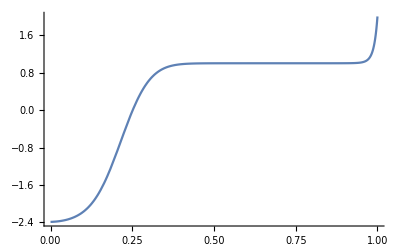

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

```mathematica
(*Outer*)
```

```mathematica
DSolve[{-(x-0.25)*(x-0.75)*y'[x]-x*(y[x]-1)==0,y[0]==-2},y[x],x]
```

```mathematica
DSolve[{-(x-1/4)*(x-3/4)*y'[x]-x*(y[x]-1)==0,y[1]==2},y[x],x]
```

{{y[x]→(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}

```mathematica
DSolve[{-(x-1/4)*(x-3/4)*y'[x]-x*(y[x]-1)==0,y[0]==-2},y[x],x]
```

{{y[x]→(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}

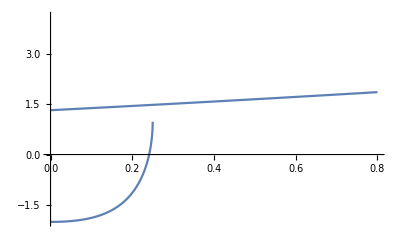

```mathematica
Show[Plot[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),{x,0,0.8}],Plot[2/3 (-3+6 ⅇ^(-3/16+(3 x)/16)),{x,0,0.8}]]
```

```mathematica
(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)/.x-> 0.80
```

259.505+0. ⅈ

```mathematica
Table[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),{x,0,1/4}]
```

{-2}

```mathematica
(*Inner solution*)
```

```mathematica
DSolve[{w''[x]-3/16w'[x]==0,w[0]==-2,w[1]==2},w[x],x]
```

{{w[x]→(2 (-1-ⅇ^(3/16)+2 ⅇ^(3 x/16)))/(-1+ⅇ^(3/16))}}

```mathematica
DSolve[{w''[x]-w[x]+1==0,w[1]==2},w[x],x]
```

{{w[x]→ⅇ^-x (ⅇ+ⅇ^x) (1-ⅇ C[1]+ⅇ^x C[1])}}

```mathematica
Simplify[ⅇ^-x (ⅇ+ⅇ^x) (1-ⅇ C[1]+ⅇ^x C[1])]
```

ⅇ^-x (ⅇ+ⅇ^x) (1-ⅇ C[1]+ⅇ^x C[1])

```mathematica
DSolve[{w''[x]-3/16w'[x]==0,w[1]==2},w[x],x]
```

{{w[x]→2/3 (3-8 ⅇ^(3/16) C[1]+8 ⅇ^(3 x/16) C[1])}}

```mathematica
{{w[x]->2/3 (3-8 ⅇ^(3/16) C[1]+8 ⅇ^(3 x/16) C[1])}}/.C[1]-> 3/(4 ⅇ^(3/16))
```

{{w[x]→2/3 (-3+6 ⅇ^(-3/16+(3 x)/16))}}

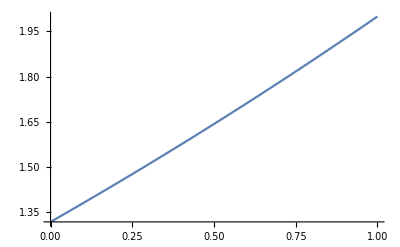

```mathematica
Plot[2/3 (-3+6 ⅇ^(-3/16+(3 x)/16)),{x,0,1}]
```

```mathematica
(*Matching*)
```

```mathematica
Limit[1,x->-Infinity]
```

1

```mathematica
Limit[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),x-> 0]
```

-2

```mathematica
FullSimplify[ⅇ^-x (ⅇ+ⅇ^x) (1-ⅇ C[1]+ⅇ^x C[1])]
```

ⅇ^-x (ⅇ+ⅇ^x) (1+(-ⅇ+ⅇ^x) C[1])

```mathematica
Limit[2/3 (3-8 ⅇ^(3/16) C[1]+8 ⅇ^(3 x/16) C[1]),x->-Infinity]
```

2-16/3 ⅇ^(3/16) C[1]

```mathematica
Limit[2/3 (3-8 ⅇ^(3/16) C[1]+8 ⅇ^(3 x/16) C[1]),x->-Infinity]-Limit[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),x-> 0]
```

```mathematica
4-16/3 ⅇ^(3/16)
```

```mathematica
Reduce[%==0,C[1]]
```

C[1]==3/(4 ⅇ^(3/16))

```mathematica
(*composite*)
```

```mathematica
Composite[x_]:=(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)+2/3 (-3+6 ⅇ^(-3/16+(3 x)/16))-2
```

```mathematica
N[Composite [1]]
```

28.

```mathematica
2/3 (-3+6 ⅇ^(-3/16+(3 x)/16))/.x-> (x-1)/ϵ
```

```mathematica
N[2/3 (-3+6 ⅇ^(-3/16+(3 (-1+x))/(16 ϵ)))]/.x-> 1/.ϵ-> 0.01
```

1.31612

```mathematica
FullSimplify[2/3 (-3+6 ⅇ^(-3/16+(3 (-1+x))/(16 ϵ)))+(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)-2]
```

```mathematica
-3+4 ⅇ^((3 (-1+x-ϵ))/(16 ϵ))-(9 √(3-12 x))/(3-4 x)^(3/2)/.ϵ-> 0.01
```

-3+4 ⅇ^(18.75 (-1.01+x))-(9 √(3-12 x))/(3-4 x)^(3/2)

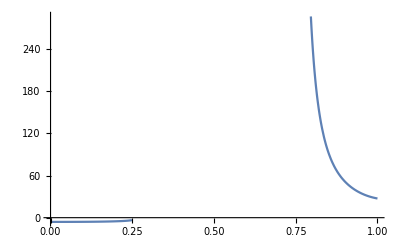

```mathematica
Plot[-3+4 ⅇ^(18.75 (-1.01+x))-(9 √(3-12 x))/(3-4 x)^(3/2),{x,0,1}]
```